# Real Analysis, Lecture #37

## Mopping Up Chapter 7: An Important Theorem about Taylor Series

Theorem 7.21 (page 268): Suppose that f is infinitely differentiable on an open interval I that contains the point c.  If there exists a positive number M such that |f^(n)(t)|≤M for all t∈I and for all positive integers n, then the function f and its Taylor series centered at c are equal for all x∈I.

Can use this theorem to show that ⅇ^x=∑ _(k=0)^∞ x^k/(k!)  ∀x∈ℝ, sin(x)=∑ _(k=0)^∞ ((-1)^(k)x^(2k+1))/((2k+1)!)  ∀x∈ℝ, and cos(x)=∑ _(k=0)^∞ ((-1)^(k)x^(2k))/((2k)!)  ∀x∈ℝ

The convergence of these series to the functions above is not uniform over all of ℝ, but it is uniform over any bounded subinterval of ℝ.

## Wait...isn’t Topology related to Geometry??

Image Credit: David Darling http://www.daviddarling.info/encyclopedia/T/topology.html

## References

An Introduction to Chaotic Dynamical Systems, 2nd Edition, Robert L. Devaney, 2003, Westview Press

Encounters with Chaos, Denny Gulick, 1992, McGraw-Hill, Inc.

Chaos and Fractals, The Mathematics Behind the Computer Graphics, Robert L. Devaney and Linda Keen, Editors, Volume 39 of Proceedings of Symposia in Applied Mathematics, 1989, American Mathematical Society

Chaos and Fractals, The Mathematics Behind the Computer Graphics, Robert L. Devaney and Linda Keen, Editors, Volume 39 of Proceedings of Symposia in Applied Mathematics, 1989, American Mathematical Society

Chaotic Spkes Arising from a Model of Bursting in Excitable Membranes, David Terman, 1991, SIAM Journal of Applied Mathematics, Volume 51, Issue 5, p. 1418-1450

## An Parable of Chaos: the Butterfly Effect

Small changes in initial conditions of certain nonlinear systems can have radical long-term effects.

Does the flap of a butterfly’s wings in Brazil set off a tornado in Texas?

Image from: http://www.themusicofalexthode.com/the-butterfly-effect/

## An Icon of Chaos: the Lorenz Attractor

Occurs for the nonlinear system of differential equations {(d x)/(d t)=σ(y-x)       
(d y)/(d t)=ρ x-y-x z
(d z)/(d t)=-β z+x y    .  Typical parameter values chosen are σ=10, ρ=28, and β=8/3.

```mathematica
axes=ParametricPlot3D[{{t,0,0},{0,t,0},{0,0,t}},{t,-1000,1000},PlotStyle->{{Thickness[.01],Black}}];Subscript[f, σ_][x_,y_,z_]:=σ*(y-x);Subscript[g, ρ_][x_,y_,z_]:=ρ*x-y-x*z;Subscript[h, β_][x_,y_,z_]:=-β*z+x*y;EqPts[σ_,ρ_,β_]:={{0,0,0},{-√β √(-1+ρ),-√β √(-1+ρ),-1+ρ},{√β √(-1+ρ),√β √(-1+ρ),-1+ρ}};Subscript[Solution, σ_,ρ_,β_][x0_,y0_,z0_]:=NDSolve[{x'[t]==Subscript[f, σ][x[t],y[t],z[t]],y'[t]==Subscript[g, ρ][x[t],y[t],z[t]],z'[t]==Subscript[h, β][x[t],y[t],z[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,100}];
```

```mathematica
Manipulate[Grid[{{Show[axes,ListPointPlot3D[EqPts[σ,ρ,β],PlotStyle->{Green,PointSize[.04]}],ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.Subscript[Solution, σ,ρ,β][x0,y0,z0]],{t,0,b},PlotStyle->Red,PlotPoints->100,PerformanceGoal->"Quality"],PlotRange->{{-30,40},{-30,40},{-20,50}},AxesLabel->{Text[Style["x",Large,Italic]],Text[Style["y",Large,Italic]],Text[Style["z",Large,Italic]]},ImageSize->300]},{Plot[{Evaluate[x[t]/.Subscript[Solution, σ,ρ,β][x0,y0,z0]],Evaluate[y[t]/.Subscript[Solution, σ,ρ,β][x0,y0,z0]],Evaluate[z[t]/.Subscript[Solution, σ,ρ,β][x0,y0,z0]]},{t,0,b},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}},PlotRange->{{0,50},{-40,40}},ImageSize->300]}}],{b,.0001,100},{{x0,0},-2,2},{{y0,1},-2,2},{{z0,0},-2,2},{{σ,10},8,12},{{ρ,28},0,40},{{β,8/3},0,5},ControlPlacement->Left,LabelStyle->Large]
```

## An Interesting Example of Chaos: Bursting in Excitable Membranes

Three-Dimensional System: ((d v)/(d t)=f_1(v,w,y)
(d w)/(d t)=f_2(v,w,y)
(d y)/(d t)=ϵ g(v,w,y),  where f_1(v,w,y)=(g_c_v(m_∞(v)))^3 h_∞(v)(v_c_a-v)+(g_k_c y/(1+y)+g_k_v w^4)(v_k-v)+g_1(v_1-v), f_2(v,w,y)=(w_∞(v)-w)/(τ_w(v)), g(v,w,y)=(α(m_∞(v)))^3 h_∞(v)(v_c_a-v)-k y, and where m_∞(v), h_∞(v), w_∞(v), and τ_w(v) have various formulae (given in the code below).

```mathematica
ϵ=.1;αm[v_]:=.1*(25+v)/(1-E^(-0.1v-2.5));βm[v_]:=4E^(-(v+50)/18);αh[v_]:=0.07E^(-0.05v-2.5);βh[v_]:=1/(1+E^(-0.1v-2));αw[v_]:=0.01*(20+v)/(1-E^(-0.1v-2));βw[v_]:=0.125E^(-(v+30)/80);m∞[v_]:=αm[v]/(αm[v]+βm[v]);h∞[v_]:=αh[v]/(αh[v]+βh[v]);w∞[v_]:=αw[v]/(αw[v]+βw[v]);τw[v_]:=(230(αw[v]+βw[v]))^(-1);τwreciprocal[v_]:=230(αw[v]+βw[v]);gcv=1800;vca=100;gkv=1700;vk=-75;gl=7;vl=-40;gkc=10;k=.02;α=.3;f1[v_,w_, y_]:=gcv*(m∞[v])^3*h∞[v]*(vca-v)+(gkc*(y/(1+y))+gkv*(w)^4)*(vk-v)+gl*(vl-v);f2[v_,w_,y_]:=(w∞[v]-w)*τwreciprocal[v];g[v_,w_,y_]:=α*(m∞[v])^3*h∞[v]*(vca-v)-k*y;solution=NDSolve[{v'[t]==f1[v[t],w[t],y[t]],w'[t]==f2[v[t],w[t],y[t]],y'[t]==ϵ*g[v[t],w[t],y[t]],v[0]==-50,w[0]==.1,y[0]==.5},{v,w,y},{t,300},MaxSteps->2000000,MaxStepSize->.001];burstVplot[T_]:=Plot[Evaluate[v[t]/.solution],{t,0,T},PlotStyle->RGBColor[1,0,0],PlotRange->{{0,100},{-50,-15}},PlotPoints->400,AxesLabel->{Text[Style["t",Large,Italic]],Text[Style["v",Large,Italic]]},ImageSize->300,PerformanceGoal->"Quality"];burstWplot[T_]:=Plot[Evaluate[w[t]/.solution],{t,0,T},PlotStyle->RGBColor[0,1,0],PlotRange->{{0,100},{0,.5}},AxesLabel->{Text[Style["t",Large,Italic]],Text[Style["w",Large,Italic]]},ImageSize->300,PerformanceGoal->"Quality"];burstYplot[T_]:=Plot[Evaluate[y[t]/.solution],{t,0,T},PlotStyle->RGBColor[0,0,1],PlotRange->{{0,100},{.5,.56}},AxesLabel->{Text[Style["t",Large,Italic]],Text[Style["y",Large,Italic]]},ImageSize->300,PerformanceGoal->"Quality"];BurstingPlot[T_]:=ParametricPlot3D[Evaluate[{v[t],w[t],y[t]}/.solution],{t,0,T},PlotStyle->{Thick,Red},PlotRange->All,BoxRatios->{.5,1,1},PlotPoints->300,PlotRange->{{-50,20},{0,.5},{.5,.56}},AxesLabel->{Text[Style["v",Large,Italic]],Text[Style["w",Large,Italic]],Text[Style["y",Large,Italic]]},ImageSize->300,PerformanceGoal->"Quality"];Manipulate[Grid[{{burstVplot[T],burstWplot[T],burstYplot[T]},{,BurstingPlot[T],}}],{T,.000001,100},LabelStyle->Large]
```

## A Preview of Chaos We Can Analyze: Interesting Graphs and Facts for the Logistic (Family of) Map(s) f_μ(x)=μ x(1-x), μ > 0

“Time series” plots

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[x, 0]=0.1;n=50;Clear[orbit];orbit[μ_]:=NestList[Subscript[f, μ],Subscript[x, 0],n];Manipulate[Show[ListPlot[orbit[μ],Joined->True,PlotStyle->Red,DataRange->{0,50}],ListPlot[orbit[μ],PlotStyle->{Black,PointSize[.02]},DataRange->{0,50}],AxesLabel->{Text[Style["n",Large,Italic]],Text[Style["x_n",Large,Italic]]},PlotRange->{-.1,1.1},AxesOrigin->{0,0}],{μ,0,4},LabelStyle->Large]
```

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[x, 0]=0.1;n=50;Clear[orbit];orbit[μ_]:=NestList[Subscript[f, μ],Subscript[x, 0],n];Manipulate[Show[ListPlot[orbit[μ],Joined->True,PlotStyle->Red,DataRange->{0,50}],ListPlot[orbit[μ],PlotStyle->{Black,PointSize[.02]},DataRange->{0,50}],AxesLabel->{Text[Style["n",Large,Italic]],Text[Style["x_n",Large,Italic]]},PlotRange->{-.1,1.1},AxesOrigin->{0,0}],{μ,3,4},LabelStyle->Large]
```

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[x, 0]=0.1;n=50;Clear[orbit];orbit[μ_]:=NestList[Subscript[f, μ],Subscript[x, 0],n];Manipulate[Show[ListPlot[orbit[μ],Joined->True,PlotStyle->Red,DataRange->{0,50}],ListPlot[orbit[μ],PlotStyle->{Black,PointSize[.02]},DataRange->{0,50}],AxesLabel->{Text[Style["n",Large,Italic]],Text[Style["x_n",Large,Italic]]},PlotRange->{-.1,1.1},AxesOrigin->{0,0}],{μ,3.4,3.6},LabelStyle->Large]
```

Cobweb plots

```mathematica
CobWebPlot[f_,{x_,xmin_,xmax_},{y_,ymin_,ymax_},seed_,iterates_]:=
	Module[{myList},
		myList=NestList[f,seed,iterates]//N;
		Plot[{f[x],x},{x,xmin,xmax},PlotStyle->{{Thick,Red},{Thick,Blue}},
Epilog->Map[{Thick,Line[{{#,#},{#,f[#]},{f[#],f[#]},{f[#],f[f[#]]}}]}&,myList],
	PlotRange->{ymin,ymax}]]
```

Fixed Points: f_μ(x)=^set x⟹μ x-μ x^2=x⟹μ x^2+(1-μ)x=0⟹x(μ x+(1-μ))=0⟹x=0,(μ-1)/μ=1-1/μ

```mathematica
Solve[μ*x-μ*x^2==x,x]
```

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Manipulate[Show[CobWebPlot[Subscript[f, μ],{x,-.1,1.2},{y,-.1,1.2},seed,n],Graphics[{Thick,Black,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}],ListPlot[{{0,0},{(μ-1)/μ,(μ-1)/μ}},PlotStyle->{Green,PointSize[.03]}],AspectRatio->Automatic],{μ,1,5},{{seed,.1},.01,.99},{n,0,50,1},LabelStyle->Large]
```

Nature of the Fixed Points: f_μ^′(x)=μ-2μ x⟹f_μ^′(0)=μ and f_μ^′((μ-1)/μ)=μ-2μ·(μ-1)/μ=μ-2(μ-1)=2-μ.

The fixed point at x=0 is an attracting fixed point if 0<μ<1 and a repelling fixed point if μ>1.  A “bifurcation” in the nature of this fixed point occurs at μ=1.

The fixed point at x=(μ-1)/μ=1-1/μ is an attracting fixed point if -1<2-μ<1, which is equivalent to 1<μ<3; and it is a repelling fixed point if 2-μ<-1, which is equivalent to μ>3.  A “bifurcation” in the nature of this fixed point occurs at μ=3.

Non-Fixed, Period-Two Points: f_μ^2(x)=f_μ(f_μ(x))=μ^2 x-(μ^2+μ^3)x^2+2 μ^3 x^3-μ^3 x^4=^set x leads to non-fixed, period-two points when μ^2-2μ-3=(μ+1)(μ-3)≥0, which is equivalent to μ≥3, at the two points x=(μ+μ^2±μ √(μ^2-2μ-3))/(2 μ^2).  A “bifurcation” in the number and type of periodic points occurs at μ=3.

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[f, μ][Subscript[f, μ][x]]//Expand
```

x μ^2-x^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3

```mathematica
Solve[x μ^2-x^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3==x,x]
```

{{x→0},{x→(-1+μ)/μ},{x→(μ+μ^2-μ √(-3-2 μ+μ^2))/(2 μ^2)},{x→(μ+μ^2+μ √(-3-2 μ+μ^2))/(2 μ^2)}}

```mathematica
{D[Subscript[f, μ][Subscript[f, μ][x]],x]/.{x->(μ+μ^2-μ √(-3-2 μ+μ^2))/(2 μ^2)}//Simplify,D[Subscript[f, μ][Subscript[f, μ][x]],x]/.{x->(μ+μ^2+μ √(-3-2 μ+μ^2))/(2 μ^2)}//Simplify}
```

{4+2 μ-μ^2,4+2 μ-μ^2}

```mathematica
{Solve[4+2μ-μ^2==1,μ],Solve[4+2μ-μ^2==-1,μ]}
```

{{{μ→-1},{μ→3}},{{μ→1-√6},{μ→1+√6}}}

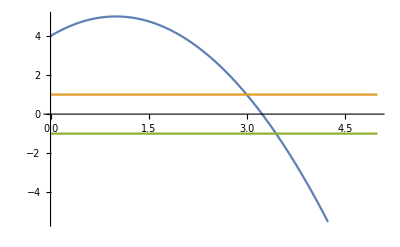

```mathematica
Plot[{4+2μ-μ^2,1,-1},{μ,0,5}]
```

The derivative of the second iterate is (f_μ^2)'(x)=μ^2-2(μ^2+μ^3)x+6 μ^3 x^2-4 μ^3 x^3.  Amazingly, (f_μ^2)'((μ+μ^2±μ √(μ^2-2μ-3))/(2 μ^2))=4+2μ-μ^2 so that the period two orbit is attracting when |4+2μ-μ^2|<1 and repelling when |4+2μ-μ^2|>1.  For μ>3, the period two orbit is attracting when μ<1+√6≈3.449489743 and repelling when μ>1+√6≈3.449489743.  A “bifurcation” in the nature of this period two orbit occurs at μ=1+√6≈3.449489743.  This also results in a bifurcation in the number of type of periodic points...an “attracting 4-cycle” is “born” at μ=1+√6≈3.449489743.

Adding in the graph of the second iterate f^2(x)=(f_μ∘f_μ)(x)=f_μ(f_μ(x))

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Manipulate[Show[CobWebPlot[Subscript[f, μ],{x,-.1,1.2},{y,-.1,1.2},seed,n],Plot[Subscript[f, μ][Subscript[f, μ][x]],{x,-.1,1.2},PlotStyle->{Thick,Magenta}],Graphics[{Thick,Black,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}],ListPlot[{{0,0},{(μ-1)/μ,(μ-1)/μ},{(μ+μ^2+μ*√(μ^2-2μ-3))/(2μ^2),(μ+μ^2+μ*√(μ^2-2μ-3))/(2μ^2)},{(μ+μ^2-μ*√(μ^2-2μ-3))/(2μ^2),(μ+μ^2-μ*√(μ^2-2μ-3))/(2μ^2)}},PlotStyle->{Green,PointSize[.03]}],AspectRatio->Automatic],{μ,1,5},{{seed,.1},.01,.99},{n,0,50,1},LabelStyle->Large]
```

For μ approximately between 3.44949 and 3.54409, the attracting 4-cycle persists until an attracting 8-cycle is “born” (at about 3.564407).  After μ increases a bit more, an attracting 16-cycle is born, then and attracting 32-cycle, then an attracting 32-cycle, etc...  The successive ratios of the length of these intervals on which these attracting cycles approach the Feigenbaum constant δ=4.66920…, which occurs “universally” in similar situations to the logistic family.

```mathematica
{(.44949)/(3.54409-3.44949),(3.54409-3.44949)/(3.564407-3.54409),(3.564407-3.54409)/(3.568750-3.564407)}
```

{4.75148,4.6562,4.6781}

For μ greater than approximately 3.56995, “chaos reigns”, for the most part...except for certain small “islands of stability”.

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[x, 0]=0.1;n=150;Clear[orbit];orbit[μ_]:=NestList[Subscript[f, μ],Subscript[x, 0],n];Manipulate[Show[ListPlot[orbit[μ],Joined->True,PlotStyle->Red,DataRange->{0,150}],ListPlot[orbit[μ],PlotStyle->{Black,PointSize[.02]},DataRange->{0,150}],AxesLabel->{Text[Style["n",Large,Italic]],Text[Style["x_n",Large,Italic]]},PlotRange->{-.1,1.1},AxesOrigin->{0,0}],{μ,3.44,3.6},LabelStyle->Large]
```

### Logistic Family Bifurcation Diagram (Picture from Wikipedia)

### A Version of the Bifurcation Diagram Made on Mathematica

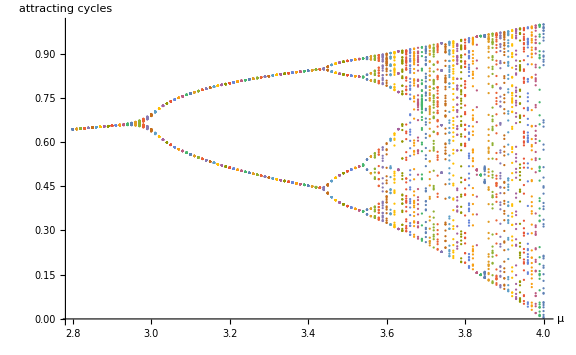

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);ListPlot[Table[Take[Transpose[{Table[μ,{i,1,101}],NestList[Subscript[f, μ],.1,100]}],-50],{μ,2.8,4,.01}],AxesLabel->{Text[Style["μ",Large]],Text[Style["attracting cycles",Large,Italic]]},ImageSize->Large]
```

### The Formulas for Higher Iterates Get Nasty

```mathematica
Subscript[f, μ_][x_]:=μ*x*(1-x);Subscript[f2, μ_][x_]:=Subscript[f, μ][Subscript[f, μ][x]];Subscript[f3, μ_][x_]:=Subscript[f, μ][Subscript[f, μ][Subscript[f, μ][x]]];Subscript[f4, μ_][x_]:=Subscript[f, μ][Subscript[f, μ][Subscript[f, μ][Subscript[f, μ][x]]]];Grid[{{Subscript[f, μ][x]},{Subscript[f2, μ][x]},{Subscript[f3, μ][x]},{Subscript[f4, μ][x]}}//Expand//Simplify,Alignment->Left]
```

-(-1+x) x μ
-(-1+x) x μ^2 (1-x μ+x^2 μ)
-(-1+x) x μ^3 (1-3 x^5 μ^4+x^6 μ^4-x μ (1+μ)-x^3 μ^3 (4+μ)+x^4 μ^3 (2+3 μ)+x^2 μ (1+μ+2 μ^2))
-(-1+x) x μ^4 (1-7 x^13 μ^11+x^14 μ^11+x^12 μ^10 (4+21 μ)-x^11 μ^10 (24+35 μ)-x μ (1+μ+μ^2)-x^9 μ^8 (10+30 μ+80 μ^2+21 μ^3)+x^10 μ^8 (2+6 μ+60 μ^2+35 μ^3)-x^3 μ^3 (4+5 μ+5 μ^2+6 μ^3+μ^4)-x^7 μ^7 (24+36 μ+60 μ^2+24 μ^3+μ^4)+x^2 μ (1+μ+3 μ^2+2 μ^3+2 μ^4)+x^8 μ^7 (6+24 μ+60 μ^2+60 μ^3+7 μ^4)-3 x^5 μ^4 (1+μ+6 μ^2+9 μ^3+6 μ^4+2 μ^5)+x^4 μ^3 (2+5 μ+5 μ^2+18 μ^3+9 μ^4+4 μ^5)+x^6 μ^4 (1+μ+6 μ^2+37 μ^3+34 μ^4+30 μ^5+4 μ^6))

## A “Toy” Model of Chaos: the Dynamics of the Shift Map on Σ_2

### Important Preliminaries

Let (X,d) be a metric space, let f:X⟶X be a map (function) of X to itself.  For k=0,1,2,3,…, let f^k be the k^th iterate of f, with k=0 corresponding to the identity map id(x)=x, k=1 corresponding to f itself, and k>1 giving rise to f∘f∘f∘···∘f, which is f composed with itself k times.  In other words, we are using the recursive equation x_(n+1)=f(x_n) k times when we define the function f^k.  Note that for all such k, we do indeed have f^k:X⟶X.

Let x_0∈X and let x_k=f^k(x_0).  The (forward) orbit of x_0 under f  is the set Orb_f(x_0)={f^k(x):k=0,1,2,3…}⊆X.  This is the same thing as the range of the sequence {x_k}_(k=0)^∞ defined by x_k=f^k(x_0).

### The metric space (Σ_2,d)

As a set, Σ_2 is the set of all sequences of 0’s and 1’s.  We can write Σ_2={x={x_k}_(k=0)^∞:x_k=0 or 1 for k=0,1,2,3,4,…}.  Technically speaking, a point in Σ_2 is a function ℕ∪{0}⟶{0,1}, though we will think of a point intuitively as an infinite list x_0 x_1 x_2 x_3 x_4…

The function d:Σ_2×Σ_2⟶[0,∞) defined by d(x,y)=d({x_k},{y_k})=∑ _(k=0)^∞ (|x_k-y_k|)/2^k is a metric (this is well-defined because the infinite series always converges by comparison with ∑ _(k=0)^∞ 1/2^k=1/(1-1/2)=2.  This also means that the outputs of d never get bigger than 2 (all “points” of this metric space (X,d) are within 2 units of distance of each other).  The function d is indeed a metric.  Verification is relatively easy.  The triangle inequality follows by the ordinary triangle inequality for real numbers |x_k-y_k|≤|x_k-z_k|+|z_k-y_k|.

The shift map σ:Σ_2⟶Σ_2 is defined by the formula σ(x_0 x_1 x_2 x_3 x_4…)=x_1 x_2 x_3 x_4… (that is, σ shifts each term to the left by one spot after deleting the first one).  For example, σ(10110111011110111110...)=0110111011110111110…

Basic Properties of the Shift Map

The shift map σ:Σ_2⟶Σ_2 is onto.  In fact, it’s two-to-one.  Given any x_1 x_2 x_3 x_4…∈Σ_2, we have σ(0 x_1 x_2 x_3 x_4…)=x_1 x_2 x_3 x_4… and σ(1 x_1 x_2 x_3 x_4…)=x_1 x_2 x_3 x_4…

The shift map σ:Σ_2⟶Σ_2 is continuous (with respect to the above metric defined on both the domain and the codomain).  Proving this requires the following lemma about the metric space (Σ_2,d)

Lemma:  Suppose x={x_k}_(k=0)^∞,y={y_k}_(k=0)^∞∈Σ_2.  The first n+1 terms of these sequences are equal (that is, x_k=y_k for k=0,1,2,…,n) if and only if d(x,y)<1/2^n.

Proof of Lemma:

(⟹) Suppose x={x_k}_(k=0)^∞,y={y_k}_(k=0)^∞∈Σ_2 with x_k=y_k for k=0,1,2,…,n.  Then d(x,y)=∑ _(k=0)^∞ (|x_k-y_k|)/2^k=∑ _(k=n+1)^∞ (|x_k-y_k|)/2^k≤1/2^(n+1)+1/2^(n+2)+1/2^(n+3)+···=(1/2^(n+1))/(1-1/2)=1/2^n.  (⟸) If x_k_0≠y_k_0 for some k_0=0,1,2,…,n, then d(x,y)=∑ _(k=0)^∞ (|x_k-y_k|)/2^k≥1/2^k_0≥1/2^n.

Proof that σ is continuous:

Let x={x_k}_(k=0)^∞∈Σ_2 and ϵ>0 be given.  To show that σ is continuous on Σ_2, it suffices to show it is continuous at x.  Towards this end, we must find a δ>0 so that if d(x,y)<δ (where y={y_k}_(k=0)^∞∈Σ_2), then d(σ(x),σ(y))<ϵ.  Choose n∈ℕ so that 1/2^n<ϵ and let δ=1/2^(n+1).  Then, if d(x,y)<δ=1/2^(n+1), it follows that the first n+2 terms of x and y are equal: x_0=y_0, x_1=y_1, x_2=y_2,…,x_(n+1)=y_(n+1).  But this means the first n+1 terms of σ(x) and σ(y) are equal: x_1=y_1, x_2=y_2,…,x_(n+1)=y_(n+1).   Hence, d(σ(x),σ(y))<1/2^n<ϵ.		Q.E.D.

Dynamic Properties of the Shift Map:  what are some properties of sequences (of sequences) generated by the recursive equation: x_(m+1)=σ(x_m) (and x_m and x_(m+1) are sequences)

A point (sequence) of the form x=x_0 x_1 x_2 x_3… x_(n-1)x_0 x_1 x_2 x_3… x_(n-1)x_0 x_1 x_2 x_3… x_(n-1)… will be periodic of period n.  There are 2^n such sequences (because there are 2 choices (zero or one) for each x_k, k=0,1,2,…,n-1).

There are infinitely many “eventually periodic” points.

Periodic points are dense in Σ_2.  That is, given an arbitrary y=y_0 y_1 y_2 y_3…∈Σ_2 and an arbitrary ϵ>0, there exists a periodic point x=x_0 x_1 x_2 x_3… x_(n-1)x_0 x_1 x_2 x_3… x_(n-1)x_0 x_1 x_2 x_3… x_(n-1)… such that d(x,y)<ϵ.  To prove this, first choose n∈ℕ so that 1/2^n<ϵ.  Then let x be defined by x_k=y_k for all k=0,1,2,…,n and then make x periodic after that (i.e., x=y_0 y_1 y_2 y_3… y_(n-1)y_0 y_1 y_2 y_3… y_(n-1)y_0 y_1 y_2 y_3… y_(n-1)…).  Then the lemma above implies that d(x,y)<1/2^n<ϵ.

There exists a point with an orbit that is dense in Σ_2.  This means that σ is “topologically transitive”.  That is, there exists a point x_0∈Σ_2 such that the sequence generated by the recursive equation x_(m+1)=σ(x_m) gets arbitrarily close to any given point of Σ_2.  One such point is x_0=(01)(00011011)(000001010100110101011111)(00000001001001001000...)…

The shift map σ exibits sensitive dependence on initial conditions on Σ_2. Basically, this means that arbitrarily close points can have completely different long-term behavior under iteration of σ.  For an arbitrary ϵ>0, we can choose n∈ℕ such that 1/2^n<ϵ and make x,y∈Σ_2 match in their first n+1 terms so that d(x,y)<ϵ. After the n+1^st term, however, we can make the terms that follow as different from each other as we like.

## A “Real” Model of Chaos: the Dynamics of the Logistic (Family of) Map(s) f_μ(x)=μ x(1-x), μ > 0, on the unit interval [0,1]

## Cantor Sets and the Invariant Cantor Set of a Logistic Map when μ>4

### Cantor Ternary Set: Definition and Properties

Construct the Cantor ternary set C by successive removal of “middle thirds”, starting with the unit interval: C_0=[0,1], C_1=[0,1/3]∪[2/3,1], C_2=[0,1/9]∪[2/9,3/9]∪[6/9,7/9]∪[8/9,1], C_3=[0,1/27]∪[2/27,3/27]∪[6/27,7/27]∪[8/27,9/27]∪[18/27,19/27]∪[20/27,21/27]∪[24/27,25/27]∪[26/27,1], …, C=∩_(n=1)^∞C_n

### Picture from Wikimedia

The Cantor ternary set C is closed, being an intersection of closed intervals.  It therefore contains all its limit points.

The Cantor ternary set C is a self-similar fractal.  Every “subpiece”, such as the subpiece in [0,1/3] or in [18/27,19/27], is similar to the original set (by just a translation and dilation of the set). Topologically speaking, this similarity transformation implies that these pieces are “homeomorphic”.

The Cantor ternary set contains the endpoints of each piece of each C_n, which is a countable set (it’s a subset of ℚ)

However, the Cantor ternary set C is actually uncountable.  In fact, the Cantor set contains exactly those real numbers in [0,1] which have a ternary (base 3) expansion containing only 0’s and 2’s (note: for those that have more than one ternary expansion, this does not mean that both such expansions contain only 0’s and 2’s)..  For instance, 0.200000…_3=2/3, 0.020000…_3=2/9, 0.220000…_3=2/3+2/9=8/9,....  Also note examples such as 0.022222…_3=2/9+2/27+2/81+···=(2/9)/(1-1/3)=2/9·3/2=1/3, 0.2020202020…_3=2/3+2/27+2/243+···=(2/3)/(1-1/9)=2/3·9/8=3/4, and 0.02020202020…_3=2/9+2/81+2/729+···=(2/9)/(1-1/9)=2/9·9/8=1/4.

The points in C can be put in one-to-one correspondence with paths through an infinite binary tree.

### Picture from Wikimedia

The Cantor ternary set is a “perfect set”.  This means every point of C is a limit point of C.  Given any point x∈C and any number r>0, (B_d(x,r) \ {x}) ∩C≠∅.  (Stated another way, C contains no isolated points).  It is also true that every point in C is a limit point of [0,1] \ C so that, in the above situation, we also have (B_d(x,r) \ {x}) ∩([0,1] \ C)≠∅  (note: d is the standard metric on ℝ, defined using absolute values d(x,y)=|x-y|).

However, the Cantor ternary set C has “zero measure”.  The total length/measure of all the open intervals taken out in the process of forming the Cantor set is 1/3+2/9+4/27+···=(1/3)/(1-2/3)=1.  Therefore, the length/measure of the Cantor set C must be zero.

In addition, the Cantor ternary set C is “totally disconnected” (it contains no intervals...if it did, then its length/measure would be positive)

### Contributed to the Wolfram Demonstrations Project by: Eric Rowland

```mathematica
Manipulate[With[{horizontalRange=Which[c-E^r<0,{0,Min[2 E^r,1]},c+E^r>1,{Max[1-2 E^r,0],1},True,{c-E^r,c+E^r}]},Graphics[{Red,Antialiasing->True,Rectangle@@{{#⟦1⟧,0},{#⟦2⟧,1}}&[#]&/@Select[Nest[Flatten[({{#1⟦1⟧,#1⟦1⟧+1/3 (#1⟦2⟧-#1⟦1⟧)},{#1⟦2⟧-1/3 (#1⟦2⟧-#1⟦1⟧),#1⟦2⟧}}&)/@#1,1]&,{{0,1}},n],Last@Union[{#⟦1⟧<horizontalRange⟦2⟧,#⟦2⟧>horizontalRange⟦1⟧}]&]},
PlotRange->{horizontalRange,{0,1}},
AspectRatio->Full, ImageSize->{478,200},Axes->If[a,{True,False},None],Ticks->If[a,{Join[Nest[#⟦1;;-1;;2⟧&,Flatten[Nest[Flatten[({{#1⟦1⟧,#1⟦1⟧+1/3 (#1⟦2⟧-#1⟦1⟧)},{#1⟦2⟧-1/3 (#1⟦2⟧-#1⟦1⟧),#1⟦2⟧}}&)/@#1,1]&,{{0,1}},n]],If[#<0,0,#]&[Round[1/Log[(Subtract@@Reverse@horizontalRange)/11/(3^-n),3]]]],{{c,Invisible[1/6]}}],Automatic},None]]],
{{n,5,"number of iterations"},0,9,1,Appearance->"Labeled"},
{{c,N[8/27],"pan"},0,1,Appearance->"Labeled"},
{{r,-2/3,"zoom"},-2/3,-10},
{{a,True,"show number line"},{True,False}},AutorunSequencing->{{1,10},{2,5},{3,5}}]
```

### Back to the Logistic Maps

```mathematica
FixedPts[μ_]:=x/.Solve[Subscript[f, μ][x]==x,x];PeriodTwoPts[μ_]:=x/.Solve[Subscript[f2, μ][x]==x,x];
PeriodThreePts[μ_]:=x/.NSolve[Subscript[f3, μ][x]==x,x,Reals];PeriodFourPts[μ_]:=x/.NSolve[Subscript[f4, μ][x]==x,x,Reals]
```

```mathematica
FixedPtsOnDiag[μ_]:=Transpose[{FixedPts[μ],FixedPts[μ]}];PeriodTwoPtsOnDiag[μ_]:=Transpose[{PeriodTwoPts[μ],PeriodTwoPts[μ]}];
PeriodThreePtsOnDiag[μ_]:=Transpose[{PeriodThreePts[μ],PeriodThreePts[μ]}];PeriodFourPtsOnDiag[μ_]:=Transpose[{PeriodFourPts[μ],PeriodFourPts[μ]}];
```

```mathematica
Manipulate[Show[Graphics[{Thick,Cyan,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}],Which[n==1,RegionPlot[0≤Subscript[f, μ][x]≤1&&0≤y≤1,{x,-.1,1.1},{y,-.1,1.1},PerformanceGoal->"Quality",PlotStyle->LightBlue],n==2,RegionPlot[0≤Subscript[f, μ][x]≤1&&0≤Subscript[f2, μ][x]≤1&&0≤y≤1,{x,-.1,1.1},{y,-.1,1.1},PerformanceGoal->"Quality",PlotStyle->LightBlue],n==3,RegionPlot[0≤Subscript[f, μ][x]≤1&&0≤Subscript[f2, μ][x]≤1&&0≤Subscript[f3, μ][x]≤1&&0≤y≤1,{x,-.1,1.1},{y,-.1,1.1},PerformanceGoal->"Quality",PlotStyle->LightBlue,PlotPoints->50],n==4,RegionPlot[0≤Subscript[f, μ][x]≤1&&0≤Subscript[f2, μ][x]≤1&&0≤Subscript[f3, μ][x]≤1&&0≤Subscript[f4, μ][x]≤1&&0≤y≤1,{x,-.1,1.1},{y,-.1,1.1},PerformanceGoal->"Quality",PlotStyle->LightBlue,PlotPoints->50]],Plot[{x,Subscript[f, μ][x],Subscript[f2, μ][x],Subscript[f3, μ][x],Subscript[f4, μ][x]},{x,-.1,1.1},PlotRange->{-.1,1.1},PlotStyle->{{Thick,Black},{Thick,Red},{Thick,Blue},{Thick,Green},{Thick,Yellow}},AspectRatio->Automatic],NumberLinePlot[PeriodFourPts[μ],Spacings->0,PlotStyle->{{Yellow,PointSize[.02]}}],ListPlot[PeriodFourPtsOnDiag[μ],PlotStyle->{{Yellow,PointSize[.02]}}],NumberLinePlot[PeriodThreePts[μ],Spacings->0,PlotStyle->{{Green,PointSize[.02]}}],ListPlot[PeriodThreePtsOnDiag[μ],PlotStyle->{{Green,PointSize[.02]}}],NumberLinePlot[PeriodTwoPts[μ],Spacings->0,PlotStyle->{{Blue,PointSize[.02]}}],ListPlot[PeriodTwoPtsOnDiag[μ],PlotStyle->{{Blue,PointSize[.02]}}],NumberLinePlot[FixedPts[μ],Spacings->0,PlotStyle->{{Red,PointSize[.02]}}],ListPlot[FixedPtsOnDiag[μ],PlotStyle->{{Red,PointSize[.02]}}],Axes->True],{μ,1,5},{n,1,4,1},LabelStyle->Large]
```

Transpose::nmtx: The first two levels of {PeriodFourPts[1],PeriodFourPts[1]} cannot be transposed.

Transpose::nmtx: The first two levels of {PeriodFourPts[1.],PeriodFourPts[1.]} cannot be transposed.

ListPlot::lpn: Transpose[{PeriodFourPts[1.],PeriodFourPts[1.]}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {PeriodFourPts[1.],PeriodFourPts[1.]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{PeriodFourPts[1.],PeriodFourPts[1.]}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: Transpose[{PeriodThreePts[1.],PeriodThreePts[1.]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Defining the “invariant Cantor set” for f_μ

For each n=0,1,2,3,…, let A_n={x∈[0,1]:f_μ^i(x)∈[0,1] for i=0,1,2,…,n butf_μ^(n+1)(x)∉[0,1]}. Let Λ=[0,1] \ ∪_(n=0)^∞A_n .  Then points that start in Λ stay in Λ under iteration of f_μ (forever).  This means that Λ is an “invariant set”.  These are the only points that don’t go off to -∞ under iteration of f_μ when μ>4.  Note that Λ is a Cantor-type set (or just “a Cantor set”, for short).

Let I_0 be the closed interval on the left side of A_0 (in [0,1]) and let I_1 be the closed interval on the right side of A_0 (in [0,1]).  Note that f_μ is increasing on I_0 and decreasing on I_1 and that f_μ(I_0)=[0,1] and f_μ(I_1)=[0,1].

## Translating between One Model of Chaos and the Other (for Purposes of Proof in the “Real” Case): a Homeomorphism which is also a Topological Conjugacy

Defining and using the “topological conjugacy” h:Λ⟶Σ_2

Given x∈Λ⊆I_0∪I_1⊆[0,1], define h:Λ⟶Σ_2 by h(x)=x_0 x_1 x_2 x_3…, where x_i=Piecewise[{{0, if f_μ^i(x)∈I_0}, {1, if f_μ^i(x)∈I_1}}]

It can be proved (with quite a lot of work), that h is (a) one-to-one (injective), (b) onto (surjective), and (c) continuous (note: (a) and (b) mean that h is a “one-to-one correspondence” (bijective)). It can also be proved that the inverse mapping h^-1:Σ_2⟶Λ is continuous.

It is also important and possible to prove that the compositions h∘f_μ and σ∘h, which both map Λ to Σ_2, are equal (they are the same function).  This is equivalent to f_μ=h^-1∘σ∘h and σ=h∘f_μ∘h^-1.  Because of this, the conjugacy acts to “translate” the behaviors of σ and f_μ back and forth between each other (they are equivalent...see below).

This is analogous to the idea of similar matrices in Linear Algebra.  Two matrices A and D are similar if there exists an invertible matrix P such that D=P^-1 A P.  In such a situation, A and D share a lot of properties (for example, they have the same eigenvalues).  Essentially, A and D represent the same linear transformation, but with respect to different coordinate systems.

If d_1(x,y)=|x-y|, these facts imply that the metric spaces (Λ,d_1) and (Σ_2,d) are homeomorphic.  They also imply that the dynamic behavior of the shift map σ on Σ_2 and the dynamic behavior of f_μ on Λ are equivalent.  That is, any dynamic properties that hold for one also hold for the other (such as the fact that periodic orbits are dense).

Another thing that the conjugacy can be used to show equivalence for is that, given a periodic point x (say, of period n) for σ in Σ_2, the point h^-1(x)∈Λ is periodic, of period n, for f_μ in Λ.  Basically, the reason is that the equation f_μ=h^-1∘σ∘h can be applied n times to say that f_μ^n=h^-1∘σ^n∘h.  Since σ^n(x)=x, it follows that f_μ^n(h^-1(x))=h^-1∘σ^n∘h(h^-1(x))=h^-1(σ^n(x))=h^-1(x).

## Summarizing Chapter 8

### Sections 8.1 & 8.5: Open and Closed Sets

#### The definitions of interior point, limit point, open set, closed set

#### Identify interior points (and non-interior points), limit points (and non-limit points), open sets (and non-open sets), closed sets (and non-closed sets) (see Exercises #1, 2, 3, 4)

#### A point is a limit point of a set iff there exists a sequence in the set converging to the point (and its proof).

#### The complement of an open set is closed and the complement of a closed set is open (and its proof)

#### The union of any collection of open sets is open and the intersection of any finite collection of open sets is open. The intersection of any collection of closed sets is closed and the union of any finite collection of closed sets is closed. (and its proof)

#### Without peeking at page 295, find an example of an intersection of a collection of open sets which is not open. Without peeking at page 295, find an example of a union of a collection of closed sets which is not closed.

#### Every open interval is an open set and every closed interval is a closed set. (be able to prove that an open interval is an open set...drawing pictures and working with inequalities is helpful here).

#### Every open set can be expressed as a union of open intervals (this is relatively easy to prove). In addition, every open set can be expressed as a countable union of disjoint open intervals (this is much harder to prove...see Theorem 8.5 and its proof on page 296).

#### Given a set E, know the definition of and be able to find the interior E^o of E, the derived set E^′ of E, and the closure E^- of E. Know that, no matter what E is, E^o is always open and both sets E^′ and E^- are always closed. (see Exercises #25, 26, 27, 35, 36)

### Section 8.2 & 8.5: Compact Sets

#### The definitions of an open cover and a finite subcover. The definition of a compact set. Examples of open covers with and/or without finite subcovers...in the context of thinking about sets E that are either compact or not (see Exercises #1a, 2, 3, 4).

#### Every compact set is closed and bounded. (understand Exercise #9...but it won’t be on the test)

#### A closed subset of a compact is compact

#### The Heine-Borel Theorem: A set of real numbers is compact iff it is closed and bounded.

### Section 8.3 & 8.5: Continuous Functions

#### A function is continuous on ℝ iff the inverse images f^-1((a,b)) are open in ℝ for all a,b∈ℝ with a<b (see Exercises #7 and 8)

#### Inverse images and direct images in general (and in relation to continuity). (see Exercises #16 and 19)

#### The direct image of a compact set under a continuous function is compact. (and its proof...see the proof in the book as well as Exercise #21).

#### Generalization of the Uniform Continuity Theorem (Theorem 8.24) (not on the test)